```mathematica
complx=Sum[Binomial[Binomial[n,2],k] * k,{k,1,10}]
```

1/2 (-1+n) n+1/2 (-1+n) n (-1+1/2 (-1+n) n)+1/4 (-1+n) n (-2+1/2 (-1+n) n) (-1+1/2 (-1+n) n)+1/12 (-1+n) n (-3+1/2 (-1+n) n) (-2+1/2 (-1+n) n) (-1+1/2 (-1+n) n)+1/48 (-1+n) n (-4+1/2 (-1+n) n) (-3+1/2 (-1+n) n) (-2+1/2 (-1+n) n) (-1+1/2 (-1+n) n)+6 Binomial[1/2 (-1+n) n,6]+7 Binomial[1/2 (-1+n) n,7]+8 Binomial[1/2 (-1+n) n,8]+9 Binomial[1/2 (-1+n) n,9]+10 Binomial[1/2 (-1+n) n,10]

```mathematica
f[n_]:=1/2 (-1+n) n+1/2 (-1+n) n (-1+1/2 (-1+n) n)+1/4 (-1+n) n (-2+1/2 (-1+n) n) (-1+1/2 (-1+n) n)+1/12 (-1+n) n (-3+1/2 (-1+n) n) (-2+1/2 (-1+n) n) (-1+1/2 (-1+n) n)+1/48 (-1+n) n (-4+1/2 (-1+n) n) (-3+1/2 (-1+n) n) (-2+1/2 (-1+n) n) (-1+1/2 (-1+n) n)+6 Binomial[1/2 (-1+n) n,6]+7 Binomial[1/2 (-1+n) n,7]+8 Binomial[1/2 (-1+n) n,8]+9 Binomial[1/2 (-1+n) n,9]+10 Binomial[1/2 (-1+n) n,10]
```

```mathematica
Expand[FunctionExpand[f[n]]]
```

(563 n^2)/1260-(2009 n^3)/2880-(104929 n^4)/1451520+(942563 n^5)/2903040+(240847 n^6)/1548288-(1819243 n^7)/11612160-(243803 n^8)/6635520+(35789 n^9)/1032192+(2698441 n^10)/371589120-(1048709 n^11)/185794560-(26651 n^12)/41287680+(8717 n^13)/15482880+(19 n^14)/589824-(233 n^15)/6193152+n^16/4128768+(11 n^17)/7741440-n^18/13762560-n^19/37158912+n^20/371589120

```mathematica
f[n]
```

{f[1],f[2],f[3],f[4],f[5],f[6],f[7],f[8],f[9],f[10],f[11],f[12],f[13],f[14],f[15],f[16],f[17],f[18],f[19],f[20]}

```mathematica
FunctionExpand[10Binomial[1/2(-1+n)n,10]]
```

((-4+n) (-3+n) (-2+n) (-1+n) n (1+n) (2+n) (3+n) (-18-n+n^2) (-16-n+n^2) (-14-n+n^2) (-10-n+n^2) (-8-n+n^2) (-4-n+n^2))/371589120

```mathematica
AsymptoticLessEqual[f[n],n^20,n-> Infinity]
```

True

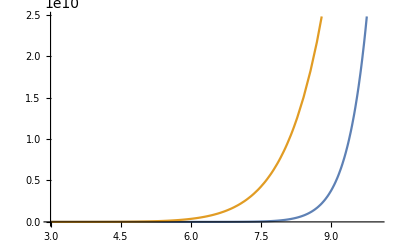

{{1,2,3,4,5},{1,2,3,5,4},{1,2,4,3,5},{1,2,4,5,3},{1,2,5,3,4},{1,2,5,4,3},{1,3,2,4,5},{1,3,2,5,4},{1,3,4,2,5},{1,3,4,5,2},{1,3,5,2,4},{1,3,5,4,2},{1,4,2,3,5},{1,4,2,5,3},{1,4,3,2,5},{1,4,3,5,2},{1,4,5,2,3},{1,4,5,3,2},{1,5,2,3,4},{1,5,2,4,3},{1,5,3,2,4},{1,5,3,4,2},{1,5,4,2,3},{1,5,4,3,2},{2,1,3,4,5},{2,1,3,5,4},{2,1,4,3,5},{2,1,4,5,3},{2,1,5,3,4},{2,1,5,4,3},{2,3,1,4,5},{2,3,1,5,4},{2,3,4,1,5},{2,3,4,5,1},{2,3,5,1,4},{2,3,5,4,1},{2,4,1,3,5},{2,4,1,5,3},{2,4,3,1,5},{2,4,3,5,1},{2,4,5,1,3},{2,4,5,3,1},{2,5,1,3,4},{2,5,1,4,3},{2,5,3,1,4},{2,5,3,4,1},{2,5,4,1,3},{2,5,4,3,1},{3,1,2,4,5},{3,1,2,5,4},{3,1,4,2,5},{3,1,4,5,2},{3,1,5,2,4},{3,1,5,4,2},{3,2,1,4,5},{3,2,1,5,4},{3,2,4,1,5},{3,2,4,5,1},{3,2,5,1,4},{3,2,5,4,1},{3,4,1,2,5},{3,4,1,5,2},{3,4,2,1,5},{3,4,2,5,1},{3,4,5,1,2},{3,4,5,2,1},{3,5,1,2,4},{3,5,1,4,2},{3,5,2,1,4},{3,5,2,4,1},{3,5,4,1,2},{3,5,4,2,1},{4,1,2,3,5},{4,1,2,5,3},{4,1,3,2,5},{4,1,3,5,2},{4,1,5,2,3},{4,1,5,3,2},{4,2,1,3,5},{4,2,1,5,3},{4,2,3,1,5},{4,2,3,5,1},{4,2,5,1,3},{4,2,5,3,1},{4,3,1,2,5},{4,3,1,5,2},{4,3,2,1,5},{4,3,2,5,1},{4,3,5,1,2},{4,3,5,2,1},{4,5,1,2,3},{4,5,1,3,2},{4,5,2,1,3},{4,5,2,3,1},{4,5,3,1,2},{4,5,3,2,1},{5,1,2,3,4},{5,1,2,4,3},{5,1,3,2,4},{5,1,3,4,2},{5,1,4,2,3},{5,1,4,3,2},{5,2,1,3,4},{5,2,1,4,3},{5,2,3,1,4},{5,2,3,4,1},{5,2,4,1,3},{5,2,4,3,1},{5,3,1,2,4},{5,3,1,4,2},{5,3,2,1,4},{5,3,2,4,1},{5,3,4,1,2},{5,3,4,2,1},{5,4,1,2,3},{5,4,1,3,2},{5,4,2,1,3},{5,4,2,3,1},{5,4,3,1,2},{5,4,3,2,1}}

```mathematica
Plot[{f[n],n^11},{n,3,10}]
Plot[{f[n],n^20,Abs[f[n]/(n^20)]},{n,9.5,999999},PlotLegends->"Expressions"]
```